### (*Battle Model*)

```mathematica
Clear[a1,a2,R,B,t]
```

```mathematica
a1= 0.0544
```

0.0544

0.0106

R'[t]==-0.0544 B[t]

B'[t]==-0.0106 R[t]

{{R[t]→InterpolatingFunction[…][t],B[t]→InterpolatingFunction[…][t]}}

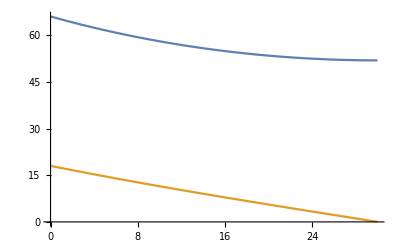

```mathematica
a2 = 0.0106
de1 = R'[t]==-a1*B[t]
de2 = B'[t]== -a2*R[t]
sol = NDSolve[{de1,de2,R[0]==66,B[0]==18},{R[t],B[t]},{t,0,20}]
Plot[Evaluate[{R[t],B[t]}/.sol],{t,0,30}]
```

#### jungle warfare

```mathematica
Clear[a1,a2,R,B,t]
```

```mathematica
a1= 0.01
```

0.01

0.01

R'[t]==-0.01 B[t] R[t]

B'[t]==-0.01 R[t]

{{R[t]→InterpolatingFunction[…][t],B[t]→InterpolatingFunction[…][t]}}

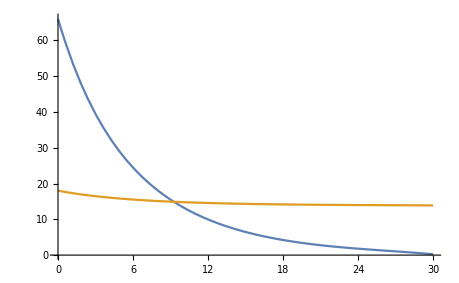

```mathematica
a2 = 0.01
de1 = R'[t]==-a1*B[t]*R[t]
de2 = B'[t]== -a2*R[t]
sol1= NDSolve[{de1,de2,R[0]==66,B[0]==18},{R[t],B[t]},{t,0,20}]
Plot[Evaluate[{R[t],B[t]}/.sol1],{t,0,30},PlotRange->All]
```

## Battle With long range weapon

```mathematica
Clear[a1,a2,R,B,t,de1,de2,sol1]
```

```mathematica
a1= 0.01
```

0.01

```mathematica
a2 = 0.01
```

0.01

R'[t]==-0.01 B[t] R[t]

B'[t]==-0.01 B[t] R[t]

{{R[t]→InterpolatingFunction[…][t],B[t]→InterpolatingFunction[…][t]}}

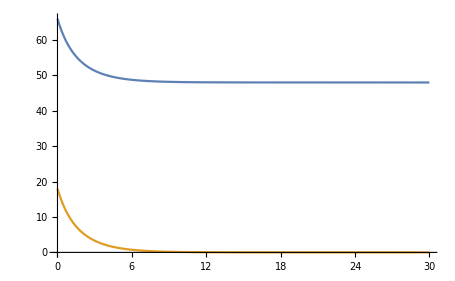

```mathematica
de1 = R'[t]==-a1*B[t]*R[t]
de2 = B'[t]== -a2*R[t]*B[t]
sol1= NDSolve[{de1,de2,R[0]==66,B[0]==18},{R[t],B[t]},{t,0,20}]
Plot[Evaluate[{R[t],B[t]}/.sol1],{t,0,30},PlotRange->All]
```